# 2. domača naloga 2025/26 - 1.del

## 1. naloga

a) Izračunajte neskončno vsoto 1+1/9+1/25+1/49+1/81+...
b) Izračunajte limito funkcije 
		f(x) = (sin(x)-x)/x^3,
    ko gre x proti 0.
c) Izračunajte ploščino lika, ki ga omejujejo graf funkcije g(x) = sin(x)+x^2, abscisna os ter navpičnici x=0 in x=2π.
d) Izračunajte ploščino lika, ki ga omejujeta grafa funkcij g(x) = sin(x)+x^2 in g1(x) = sin(x) + x^5/5.

```mathematica
Sum[1/(2 n -1)^2,{n,1,Infinity}]
```

π^2/8

```mathematica
Limit[(Sin[x]-x)/x^3,x->0]
```

-1/6

```mathematica
Integrate[Abs[Sin[x]+x^2],{x,0,2 Pi}]
```

(8 π^3)/3

```mathematica
(*Izračun presečišča*)
Solve[Sin[x]+x^2==Sin[x]+x^5/5,x, Reals]//N
```

{{x→0.},{x→0.},{x→1.70998}}

```mathematica
Integrate[Abs[(Sin[x]+x^2)-(Sin[x]+x^5/5)],{x,0,5^(1/3)}]
```

5/6

Syntax::bktmcp: Expression "Abs[Sin[x]+bx^2" has no closing "]".

## 2. naloga

a)  Definirajte funkcijo A(m,n), ki sprejme naravni števili  in  in vrne matriko dimenzije , kjer se na vsakem mestu v matriki pojavi vsota indeksa stolpca in indeksa vrstice.
b) Izračunajte determinanto, rang in lastne vrednosti matrike . Kaj opazite?
c)  Narišite vektorje, ki ustrezajo stolpcem matrike . S pomočjo ukaza InfinitePlane na sliko narišite še ravnino, v kateri ti trije vektorji ležijo. 
d) Določite parametra, s katerima lahko prvi stolpec matrike A(3,3) izrazimo z drugima dvema.
e) Določite cela števila α, x_1,x_2 in x_3, ki zadoščajo enakosti 
		M (x_1
x_2
x_3) = (-3
-5
-9
-11) ,
    kjer je M matrika, podana kot A(4,3)+αI, kjer I označuje identično matriko ustrezne velikosti. Rešitev zapišite v eni vrstici.

```mathematica
A[m_,n_]:=Table[i+j,{i,n},{j,m}]
```

```mathematica
mat=A[3,3];
```

```mathematica
Det[mat]
```

0

```mathematica
MatrixRank[mat]
```

2

```mathematica
Eigenvalues[mat]
```

{6+√42,6-√42,0}

```mathematica
v1={2,3,4};
```

```mathematica
v2={3,4,5};
```

```mathematica
v3={4,5,6};
```

```mathematica
Graphics3D[{Arrow[{{0,0,0},v1}],Arrow[{{0,0,0},v2}],Arrow[{{0,0,0},v3}], InfinitePlane[{v1,v2,v3}]}]
```

-Graphics3D-

```mathematica
Solve[v1==a v2+b v3,{a,b}]
```

{{a→2,b→-1}}

```mathematica
M=A[3,3]+α IdentityMatrix[3];
```

```mathematica
Solve[M.{x1,x2,x3}=={-3,-5,-9},{α,x1,x2,x3},Integers]
(*Tukaj matriko M pomnožimo z desnim stolpčnim vektorjem neznank. Rezultat tega množenja je nov sistem treh enačb, kjer imamo na desni strani vektor rezultatov.*)
```

{{α→-2,x1→-1,x2→-1,x3→0}}

## 3. naloga

V datoteki ‘vreme.xlsx’ se nahajajo podatki o najvišjih in povprečnih mesečnih temperaturah v Ljubljani v letu 2025. Podatke uvozite v Mathematico.

a) Grafično predstavite podatke o najvišjih mesečnih temperaturah (graf naj bo čim bolj podoben spodnjemu). Pri tem vrednosti temperatur in številke mesecev z ustreznimi poizvedbami preberite iz uvožene tabele.
b) Napišite poizvedbo, ki bo vrnila imena ‘toplih mesecev’ - to so tisti meseci, katerih povprečna temperatura je višja ob 15 stopinj. Poizvedbo poskusite napisati v eni vrstici.

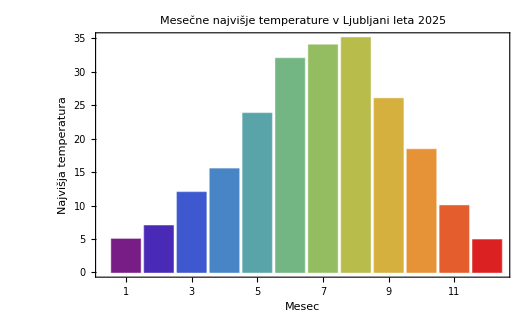

```mathematica
SetDirectory[NotebookDirectory[]];
podatki=Import["vreme.xlsx","Data"]
```

{{{Številka,Mesec,Najvišja,Povprečna},{1.,Januar,5.,2.5},{2.,Februar,7.,2.},{3.,Marec,12.,8.},{4.,April,15.5,12.2},{5.,Maj,23.8,15.3},{6.,Junij,32.,22.9},{7.,Julij,34.,21.8},{8.,Avgust,35.1,21.6},{9.,September,26.,17.4},{10.,Oktober,18.4,10.6},{11.,November,10.,6.6},{12.,December,4.9,3.7}}}

```mathematica
tabela=podatki[[1]];
```

```mathematica
(*Iz uvoženega Excelovega dokumenta vzame prvi delovni list*)
```

```mathematica
meseci=tabela[[2;;,1]];
(*pomeni:vzemi vse vrstice od druge naprej (s čimer elegantno preskočiš glavo tabele,da ne uvoziš besedila "Številka").*)
```

```mathematica
temp=tabela[[2;;,3]];
(*Izlušči najvišje mesečne temperature.
2;; ponovno preskoči prvo vrstico z naslovi.
,3 vzame podatke iz tretjega stolpca (stolpec "Najvišja").*)
```

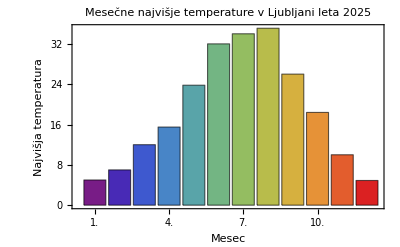

```mathematica
BarChart[temp,(*Podatki za višino stolpcev-najvišje temperature*)
ChartLabels->meseci,(*Oznake pod stolpci (številke mesecev)*)Frame->True,(*pravokotni okvir okoli celotnega grafa*)Axes->False,(*Izklopi privzeto notranjo os,da se ne prekriva z okvirjem*)FrameLabel->{(*Nastavi napise na zunanjem robu okvirja*)"Mesec",(*Napis na X osi*)"Najvišja temperatura" (*Napis na Y osi*)},PlotLabel->"Mesečne najvišje temperature v Ljubljani leta 2025",(*Glavni naslov grafa*)ChartStyle->"Rainbow"  (*Obarva stolpce v mavrične barve*)]
```

```mathematica
(*S funkcijo Cases poiščemo in izluščimo podatke,ki ustrezajo specifičnemu vzorcu in pogoju*)

Cases[tabela[[2;;]],
(*1. Vzamemo tabelo s podatki pri čemer izpustimo 1. vrstico z naslovi*)

{_,mesec_,_,temp_} 
(*2. Definiramo vzorec za vrstico: 1. in 3. stolpec ignoriramo (_),2. stolpec shranimo kot'mesec', 4. stolpec kot'temp'*)

/;temp>15 
(*3. Pogojni operator:vzorec je veljaven le,ČE je vrednost v 'temp' (4. stolpec) strogo večja od 15*)

:>mesec 
(*4. Zakasnjena puščica (RuleDelayed):če vrstica ustreza pogoju,namesto celotne vrstice vrni le vrednost'mesec'*)]
```

{Maj,Junij,Julij,Avgust,September}